0.0145983

0.7116

32.1216

-7.40654

-56.8657

-0.488586

-59.6897

39.9438

62.3964

57.796

11.089

-12.8702

-26.2729

0.0041181+0.34769 Cos[θ]+10.1309 (-1+3 Cos[θ]^2)-2.76395 (-3 Cos[θ]+5 Cos[θ]^3)-6.01557 (3-30 Cos[θ]^2+35 Cos[θ]^4)-0.0571403 (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)-3.79443 (-5+105 Cos[θ]^2-315 Cos[θ]^4+231 Cos[θ]^6)+2.72753 (-35 Cos[θ]+315 Cos[θ]^3-693 Cos[θ]^5+429 Cos[θ]^7)+0.566982 (35-1260 Cos[θ]^2+6930 Cos[θ]^4-12012 Cos[θ]^6+6435 Cos[θ]^8)+0.555213 (315 Cos[θ]-4620 Cos[θ]^3+18018 Cos[θ]^5-25740 Cos[θ]^7+12155 Cos[θ]^9)+0.055996 (-63+3465 Cos[θ]^2-30030 Cos[θ]^4+90090 Cos[θ]^6-109395 Cos[θ]^8+46189 Cos[θ]^10)-0.0680149 (-693 Cos[θ]+15015 Cos[θ]^3-90090 Cos[θ]^5+218790 Cos[θ]^7-230945 Cos[θ]^9+88179 Cos[θ]^11)-0.0361887 (231-18018 Cos[θ]^2+225225 Cos[θ]^4-1021020 Cos[θ]^6+2078505 Cos[θ]^8-1939938 Cos[θ]^10+676039 Cos[θ]^12)

-Graphics3D-

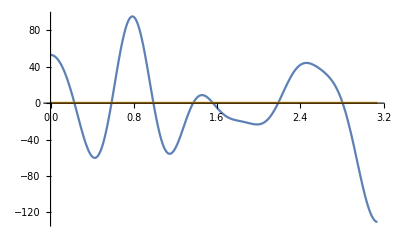

```mathematica
m1Y00=0.0145983
m1Y01=0.7116
m1Y02=32.1216
m1Y03=-7.40654
m1Y04=-56.8657
m1Y05=-0.488586
m1Y06=-59.6897
m1Y07=39.9438
m1Y08=62.3964
m1Y09=57.796
m1Y010=11.089
m1Y011=-12.8702
m1Y012=-26.2729

m1[x_]=m1Y00*SphericalHarmonicY[0,0,θ,0]+m1Y01*SphericalHarmonicY[1,0,θ,0]+m1Y02*SphericalHarmonicY[2,0,θ,0]+m1Y03*SphericalHarmonicY[3,0,θ,0]+m1Y04*SphericalHarmonicY[4,0,θ,0]+m1Y05*SphericalHarmonicY[5,0,θ,0]+m1Y06*SphericalHarmonicY[6,0,θ,0]+m1Y07*SphericalHarmonicY[7,0,θ,0]+m1Y08*SphericalHarmonicY[8,0,θ,0]+m1Y09*SphericalHarmonicY[9,0,θ,0]+
m1Y010*SphericalHarmonicY[10,0,θ,0]+m1Y011*SphericalHarmonicY[11,0,θ,0]+m1Y012*SphericalHarmonicY[12,0,θ,0]

SphericalPlot3D[{(1/1.7470297728681317)*m1[θ], 1/(2 √π)},{θ,0,π},{ϕ,0,π}, PlotRange -> All]
Plot[{m1[θ],1/(2 √π)},{θ,0,π}, PlotRange -> All]
```

```mathematica
Show[%724,ViewPoint->{0,-∞,0}]
```

```mathematica
SphericalPlot3D[{ 1*SphericalHarmonicY[0,0,θ,0],SphericalHarmonicY[2,0,θ,0]  },{θ,0,Pi},{ϕ,0,Pi}, PlotRange -> All]
```

-Graphics3D-

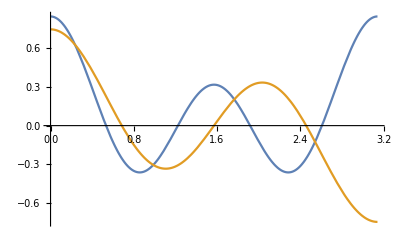

```mathematica
Plot[{ SphericalHarmonicY[4,0,θ,0],SphericalHarmonicY[3,0,θ,0] },{θ,0,Pi}, PlotRange -> All]
```

```mathematica
Integrate[Sin[θ](m1[x_]), {θ,0,Pi},{ϕ,0,2 Pi}]
```

0.0517496

```mathematica
1/1.7470297728681317
```

```mathematica
1/1.7636908390672943
```

0.566993

```mathematica
Integrate[Sin[θ](SphericalHarmonicY[0,0,θ,ϕ]), {θ,0,Pi},{ϕ,0,2 Pi}]
```

```mathematica
1/(2 √π)
```

```mathematica
1/1.7695328469596348
```

0.565121

```mathematica
1/0.30019377340327935
```

3.33118

```mathematica
1/-0.04448930063925616
```

-22.4773

```mathematica
Integrate[Sin[θ](SphericalHarmonicY[0,0,θ,ϕ]*SphericalHarmonicY[5,0,θ,ϕ]), {θ,0,Pi},{ϕ,0,2 Pi}]
```

0

```mathematica
SphericalHarmonicY[0,0,θ,ϕ]^2
```

1/(4 π)

```mathematica
Simplify[(3/(4 π))^(1/3)]
```

(3/π)^(1/3)/2^(2/3)

```mathematica
N[2 √π]
```

3.54491